## DelaunayEdges-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 04:53:30
using xCellerator 0.90 and XSSA 1204002

Create a tissue with a point and an edge that aren't used.

Generate a square tissue object with randomized centers

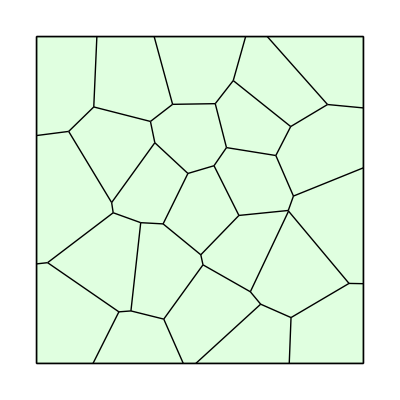

```mathematica
q=TemplateRandomSquareGrid[25, {0,0}, {10, 10}];
ShowTissue[q]
```

Find the centroids of the cells

```mathematica
v=Centroid[q]
```

{{0.988565,1.3448},{2.08856,3.13484},{0.88035,5.12783},{2.3331,6.64512},{0.851222,8.61494},{3.11623,0.671297},{3.83846,2.85446},{3.49545,5.34194},{4.70446,6.97687},{2.87483,8.74659},{5.22576,1.51855},{6.35312,3.54999},{5.04202,4.69921},{6.51377,7.36201},{4.96978,9.08162},{6.68323,0.699691},{7.92298,2.78045},{6.65466,5.55318},{8.75904,6.60017},{7.3152,8.6262},{8.98781,1.03835},{9.15946,4.32512},{8.929,9.10179}}

Find the Delaunay Triangulation of the centroids

```mathematica
de=DelaunayEdges[v]
```

{{{0.988565,1.3448},{2.08856,3.13484}},{{0.988565,1.3448},{0.88035,5.12783}},{{0.988565,1.3448},{3.11623,0.671297}},{{2.08856,3.13484},{0.88035,5.12783}},{{2.08856,3.13484},{3.11623,0.671297}},{{2.08856,3.13484},{3.83846,2.85446}},{{2.08856,3.13484},{3.49545,5.34194}},{{0.88035,5.12783},{2.3331,6.64512}},{{0.88035,5.12783},{0.851222,8.61494}},{{0.88035,5.12783},{3.49545,5.34194}},{{2.3331,6.64512},{0.851222,8.61494}},{{2.3331,6.64512},{3.49545,5.34194}},{{2.3331,6.64512},{4.70446,6.97687}},{{2.3331,6.64512},{2.87483,8.74659}},{{0.851222,8.61494},{2.87483,8.74659}},{{0.851222,8.61494},{4.96978,9.08162}},{{3.11623,0.671297},{3.83846,2.85446}},{{3.11623,0.671297},{5.22576,1.51855}},{{3.11623,0.671297},{6.68323,0.699691}},{{3.83846,2.85446},{3.49545,5.34194}},{{3.83846,2.85446},{5.22576,1.51855}},{{3.83846,2.85446},{6.35312,3.54999}},{{3.83846,2.85446},{5.04202,4.69921}},{{3.49545,5.34194},{4.70446,6.97687}},{{3.49545,5.34194},{5.04202,4.69921}},{{4.70446,6.97687},{2.87483,8.74659}},{{4.70446,6.97687},{5.04202,4.69921}},{{4.70446,6.97687},{6.51377,7.36201}},{{4.70446,6.97687},{4.96978,9.08162}},{{4.70446,6.97687},{6.65466,5.55318}},{{2.87483,8.74659},{4.96978,9.08162}},{{5.22576,1.51855},{6.35312,3.54999}},{{5.22576,1.51855},{6.68323,0.699691}},{{6.35312,3.54999},{5.04202,4.69921}},{{6.35312,3.54999},{6.68323,0.699691}},{{6.35312,3.54999},{7.92298,2.78045}},{{6.35312,3.54999},{6.65466,5.55318}},{{6.35312,3.54999},{9.15946,4.32512}},{{5.04202,4.69921},{6.65466,5.55318}},{{6.51377,7.36201},{4.96978,9.08162}},{{6.51377,7.36201},{6.65466,5.55318}},{{6.51377,7.36201},{8.75904,6.60017}},{{6.51377,7.36201},{7.3152,8.6262}},{{4.96978,9.08162},{7.3152,8.6262}},{{4.96978,9.08162},{8.929,9.10179}},{{6.68323,0.699691},{7.92298,2.78045}},{{6.68323,0.699691},{8.98781,1.03835}},{{7.92298,2.78045},{8.98781,1.03835}},{{7.92298,2.78045},{9.15946,4.32512}},{{6.65466,5.55318},{8.75904,6.60017}},{{6.65466,5.55318},{9.15946,4.32512}},{{8.75904,6.60017},{7.3152,8.6262}},{{8.75904,6.60017},{9.15946,4.32512}},{{8.75904,6.60017},{8.929,9.10179}},{{7.3152,8.6262},{8.929,9.10179}},{{8.98781,1.03835},{9.15946,4.32512}},{{9.15946,4.32512},{8.929,9.10179}}}

Plot the Delaunay Triangulation of the Centroids, and observe that the Delaunay of the centroids is not the same as the connectivity - there may be a msising or extra connection.

```mathematica
deCentroids=Graphics[Join[Point/@v, Line/@de]];
```

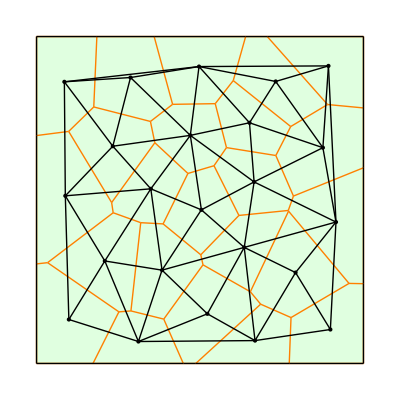

```mathematica
Show[ShowTissue[q, "EdgeStyles"-> Orange], deCentroids]
```

Observe that the Voronoi of the centroids is not the same as the original tissue.

```mathematica
bcv=BoundedCellVoronoi[v];
```

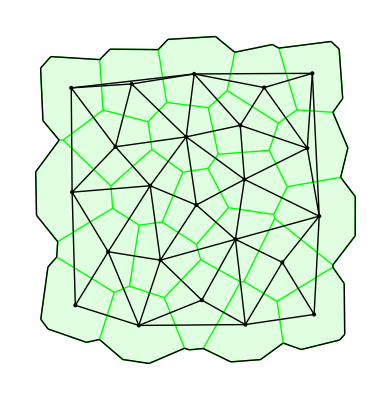

```mathematica
Show[ShowTissue[bcv, "EdgeStyles"-> Green], deCentroids]
```

#### Overlay the Voronoi Boundarys (purple, dotted) on the actual tissue

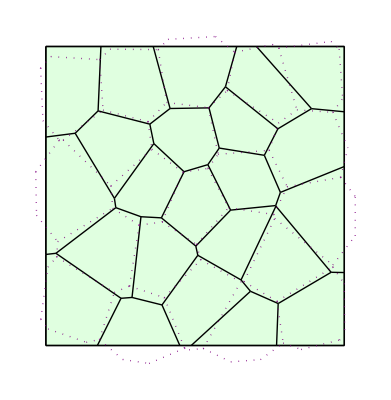

```mathematica
Show[ShowTissue[q], Graphics[{Purple, Dotted, Line/@EdgeVertices[bcv]}]]
```